General::prng: Value of option PlotRange -> {{0,180},{}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

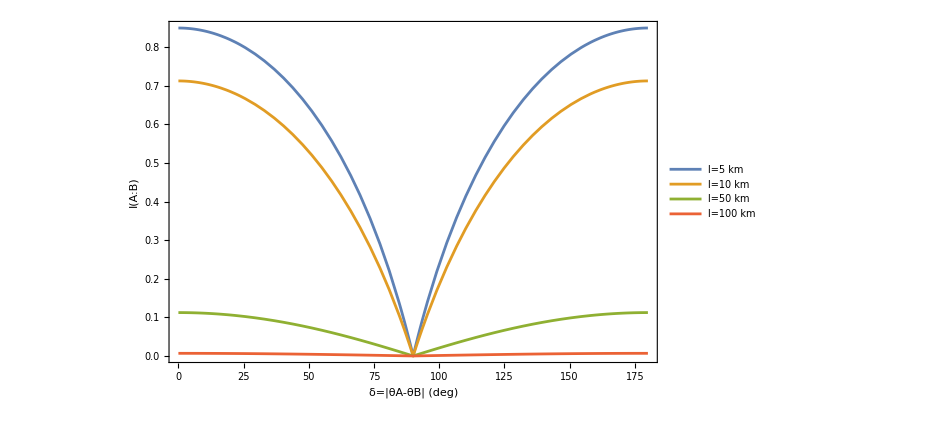

```mathematica
(*Mathematica Code for Figure 4 in `CV QKD with Single Quadrature Measurement at Arbitrary Reference Frame'*)
V:=2
Va :=V+1
ξ:=0.001
t[l_]:=10^(-0.025*l)
max:= 90
θA:= 0(*RandomInteger[{0,10}]*)
θB[δ_]:=Abs[θA-δ] 
m :=Cos[θA Degree]
Vb[δ_] :=Va*Abs[(Cos[θB[δ] Degree]/Cos[θA Degree])]
SNR[l_,δ_]:= (t[l] * (Vb[δ]))/(1+ξ)
IAB[l_,δ_]:=1/2 Log2[1+SNR[l,δ]]
(*IAB[δ_,l_]:=t[l]*(Vb[δ]-1)*)
list:=List[5,10,50,100]
(*Plot[δ1,{θB,0,90},PlotRange->{{0,max},{}}]*)
Plot[Evaluate[Table[IAB[l,δ],{l,list}]],{δ,0,180},PlotRange->{{0,180},{}},Frame->True,FrameLabel->{{HoldForm["I(A:B)"],None},{HoldForm["δ=|θA-θB| (deg)"],None}},LabelStyle->{Directive[Black,24]},PlotLegends->Placed[{"l=5 km","l=10 km","l=50 km","l=100 km"},{Center,Top}]]
```

0.749894

0

General::prng: Value of option PlotRange -> {{0,180},{}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

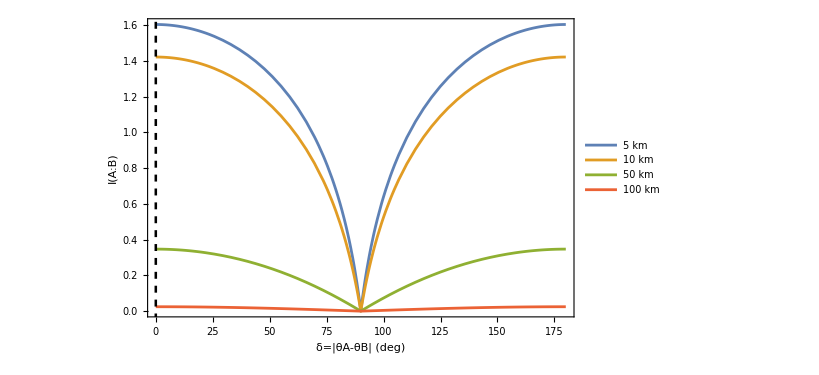

```mathematica
V:=10
Va :=V+1
ξ:=0.001
l1:=5
l2:=10
l3:=50
l4:=100
t1=10^(-0.025*l1)
t2:=10^(-0.025*l2)
t3:=10^(-0.025*l3)
t4:=10^(-0.025*l4)
max:= 90
θA= 0(*RandomInteger[{0,max}]*)
θB:=Abs[δ-θA]
m :=Cos[θA Degree]
Vb :=Va*Abs[(Cos[θB Degree]/Cos[θA Degree])]
SNR1:= (t1* (Vb))/(1+ξ)
SNR2:= (t2* (Vb))/(1+ξ)
SNR3:= (t3* (Vb))/(1+ξ)
SNR4:= (t4* (Vb))/(1+ξ)
IAB1:=1/2 Log2[1+SNR1]
IAB2:=1/2 Log2[1+SNR2]
IAB3:=1/2 Log2[1+SNR3]
IAB4:=1/2 Log2[1+SNR4]
IAB1a:=t1*(Vb-1)+ξ + 1
IAB2a:=t2*(Vb-1)+ξ + 1
IAB3a:=t3*(Vb-1)+ξ + 1
IAB4a:=t4*(Vb-1)+ξ + 1
(*Plot[δ,{θB,0,90},PlotRange->{{0,max},{}}]*)
test=With[{x0=θA,tickf={#,StringJoin[ToString[#],"°"]}&},Plot[{IAB1,IAB2,IAB3,IAB4},{δ,0,180},Frame->True,FrameLabel->{"δ=|θA-θB| (deg)","I(A:B)"},LabelStyle->{Directive[Black,20]},PlotRange->{{0,180},{}},PlotLegends->Placed[{"5 km","10 km","50 km","100 km"},{Center,Top}],Ticks->{tickf/@FindDivisions[{0,90,10},9],Automatic},GridLines->{{x0},{}},GridLinesStyle->Directive[Black, Dashed,Thickness[0.003]]]]
```